```mathematica
toFixedWidth[n_Integer,width_Integer]:=StringJoin[PadLeft[Characters[ToString[n]],width,"0"]];
toNumberedFileName[n_Integer]:=ToString@StringForm["``",toFixedWidth[n,2]];

list = {};

Do[SetDirectory[NotebookDirectory[]];
fileName = "dc_k_sl_1000_"<>toNumberedFileName[i]<>".txt";
data = ReadList[fileName, Number, RecordLists->True];
(*data = Append[data,{0.0001,0.0001}];*)
model = 1-a/x^b;
fit = FindFit[data, model, {a,b}, x];
list = Append[list,{i,b /. fit}];
modelf = Function[{x}, Evaluate[model /. fit]];
p1 = Show[ListPlot[data,PlotStyle->Red,PlotRange->{0,1}],Plot[modelf[x],{x,0,1000},PlotStyle->Black,PlotRange->{0,1}]];
(* Plot Residual Graph *)
{t,u} = Transpose[data];
residuals = u - Map[modelf,t];
p2 = ListPlot[residuals,Filling->Axis,DataRange->{Min[t],Max[t]}];

logdata1 = Map[(#*{1,-1}+{0,1})&,data];
logdata = Map[Log, logdata1, {2}];
pLog = Show[ListPlot[logdata,PlotStyle->Red,PlotRange->Automatic]];

(* Export Equation and Graphs *)
Export[StringTake[fileName,{1,-5}]<>"_fit.png",p1];
Export[StringTake[fileName,{1,-5}]<>"_res.png",p2];
Export[StringTake[fileName,{1,-5}]<>"_log.png",pLog];
Export[StringTake[fileName,{1,-5}]<>"_rlt.txt", modelf],{i,30}];

(* Try to fit the b's found from above to a curve *)
(*list = Take[list, 10];*)
modelb = a*ⅇ^(b*x);
fitb = FindFit[list, modelb, {a,b},x];
modelfb = Function[{x}, Evaluate[modelb/. fitb]];
p1b = Show[ListPlot[list,PlotStyle->Red,PlotRange->{0,1}],Plot[modelfb[x],{x,0,30},PlotStyle->Black,PlotRange->{0,1}]];
Export["dc_k_sl_1000_whatis_b.png",p1b];
Export["dc_k_sl_1000_whatis_b.txt",modelfb];
```

```mathematica
(*model=1+1/(a x+b)+Sqrt[a x+b];
fit=FindFit[data,model,{a,b},x]
modelf=Function[{x},Evaluate[model/.fit]]
Plot[modelf[x],{x,1,100},Epilog->Map[Point,data]]
Show[ListPlot[data,PlotStyle->Red,PlotRange->{0,1}],Plot[modelf[x],{x,0,100},PlotStyle->Black,PlotRange->{0,1}]]*)
```

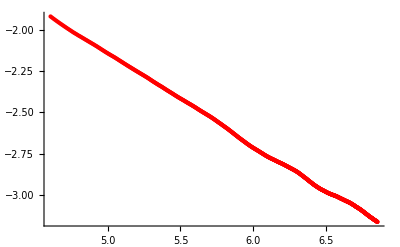

```mathematica
(*SetDirectory[NotebookDirectory[]];
fileName = "dc_k_sl_1000_01.txt";
logdata1 = Map[(#*{1,-1}+{0,1})&,ReadList[fileName, Number, RecordLists->True]];
logdata = Map[Log, data1, {2}];
Show[ListPlot[logdata,PlotStyle->Red,PlotRange->{-1,-4}]]*)
```